fsoc of minumazation point with q > 0

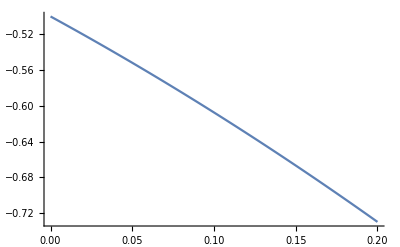
{-Graphics-,-Graphics-}

fsoc of minumazation point with q < 0

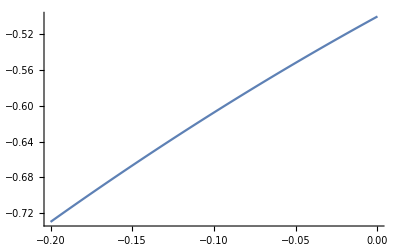
{-Graphics-,-Graphics-}

```mathematica
Clear[γ3,q,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[q_]=-1/2 (1+Abs[q])^2 Cos[2 θ0]-(1+Abs[q])q Sin[θ0];
fsoc2[q_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ0)]-(1+Abs[q])q Sin[π-θ0];
Print[Style["fsoc of minumazation point with q > 0",18,Red]];
{Plot[fsoc1[q],{q,0,0.2}],Plot[fsoc2[q],{q,0,0.2}]}
Print[Style["fsoc of minumazation point with q < 0",18,Red]];
{Plot[fsoc1[q],{q,-0.2,0}],Plot[fsoc2[q],{q,-0.2,0}]}
```

fsoc with different angles of π-soliton q=0.01

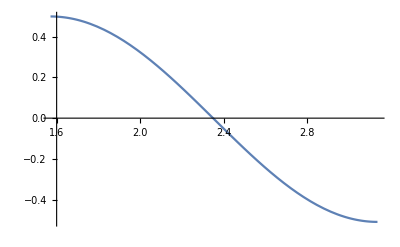
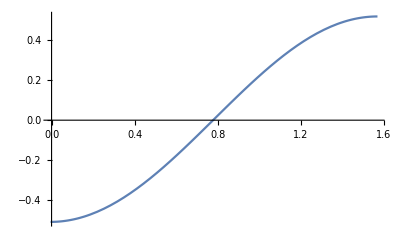

```mathematica
Clear[γ3,q,θ,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[θ_]=-1/2 (1+Abs[q])^2 Cos[2 θ]-(1+Abs[q])q Sin[θ];
fsoc2[θ_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ)]-(1+Abs[q])q Sin[π-θ];
Print[Style["fsoc with different angles of π-soliton q=0.01",18,Red]]
{Plot[fsoc1[θ]/.q->0.01,{θ,π/2,π-(θ0/.q->0.01)}],Plot[fsoc1[θ]/.q->-0.01,{θ,θ0/.q->-0.01,π/2}]}
```

fsoc with different angles of π-soliton q=0.11

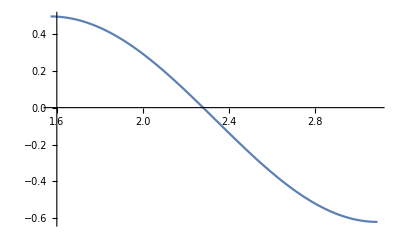
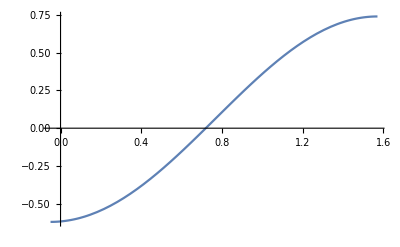

```mathematica
Clear[γ3,q,θ,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[θ_]=-1/2 (1+Abs[q])^2 Cos[2 θ]-(1+Abs[q])q Sin[θ];
fsoc2[θ_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ)]-(1+Abs[q])q Sin[π-θ];
Print[Style["fsoc with different angles of π-soliton q=0.11",18,Red]]
{Plot[fsoc1[θ]/.q->0.11,{θ,π/2,π-(θ0/.q->0.11)}],Plot[fsoc1[θ]/.q->-0.11,{θ,θ0/.q->-0.11,π/2}]}
```

fsoc with different angles of π-soliton q=0.20

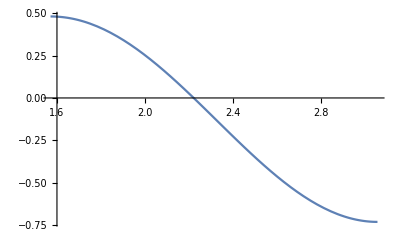
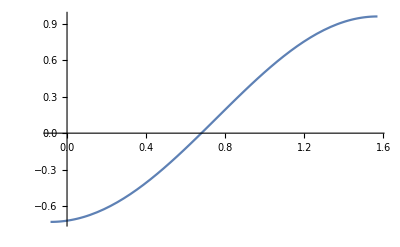

```mathematica
Clear[γ3,q,θ,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[θ_]=-1/2 (1+Abs[q])^2 Cos[2 θ]-(1+Abs[q])q Sin[θ];
fsoc2[θ_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ)]-(1+Abs[q])q Sin[π-θ];
Print[Style["fsoc with different angles of π-soliton q=0.20",18,Red]]
{Plot[fsoc1[θ]/.q->0.2,{θ,π/2,π-(θ0/.q->0.2)}],Plot[fsoc1[θ]/.q->-0.2,{θ,θ0/.q->-0.2,π/2}]}
```

fsoc with different angles of Separeble-soliton q=0.01, KLS-soliton part

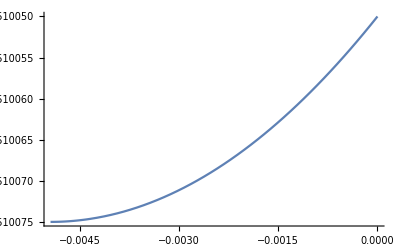
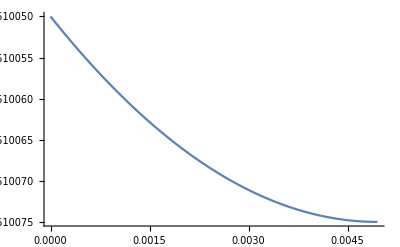

fsoc with different angles of Separeble-soliton q=0.01, soliton part

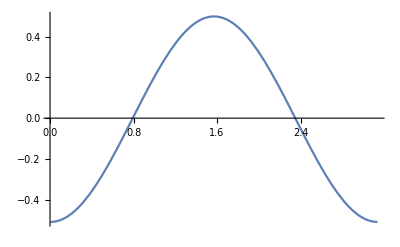

```mathematica
Clear[γ3,q,θ,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[θ_]=-1/2 (1+Abs[q])^2 Cos[2 θ]-(1+Abs[q])q Sin[θ];
fsoc2[θ_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ)]-(1+Abs[q])q Sin[π-θ];
Print[Style["fsoc with different angles of Separeble-soliton q=0.01, KLS-soliton part",18,Red]]
{Plot[fsoc1[θ]/.q->-0.01,{θ,(θ0/.q->-0.01),0}],Plot[fsoc1[θ]/.q->0.01,{θ,0,θ0/.q->0.01}]}
Print[Style["fsoc with different angles of Separeble-soliton q=0.01, soliton part",18,Red]]
{Plot[fsoc1[θ]/.q->0.01,{θ,(θ0/.q->0.01),π-(θ0/.q->0.01)}]}
```

fsoc with different angles of Separeble-soliton q=0.11, KLS-soliton part

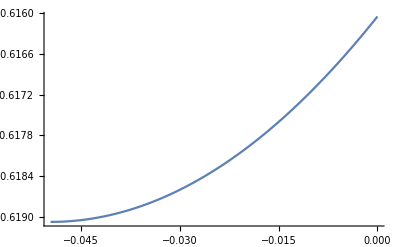
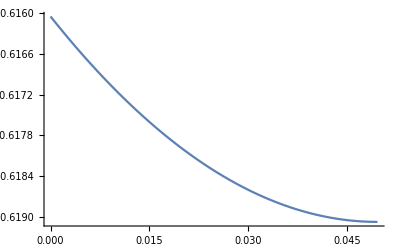

fsoc with different angles of Separeble-soliton q=0.01, soliton part

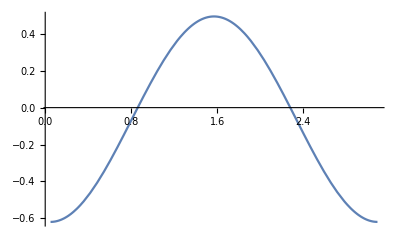

```mathematica
Clear[γ3,q,θ,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[θ_]=-1/2 (1+Abs[q])^2 Cos[2 θ]-(1+Abs[q])q Sin[θ];
fsoc2[θ_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ)]-(1+Abs[q])q Sin[π-θ];
Print[Style["fsoc with different angles of Separeble-soliton q=0.11, KLS-soliton part",18,Red]]
{Plot[fsoc1[θ]/.q->-0.11,{θ,(θ0/.q->-0.11),0}],Plot[fsoc1[θ]/.q->0.11,{θ,0,θ0/.q->0.11}]}
Print[Style["fsoc with different angles of Separeble-soliton q=0.01, soliton part",18,Red]]
{Plot[fsoc1[θ]/.q->0.11,{θ,(θ0/.q->0.11),π-(θ0/.q->0.11)}]}
```

fsoc with different angles of Separeble-soliton q=0.20, KLS-soliton part

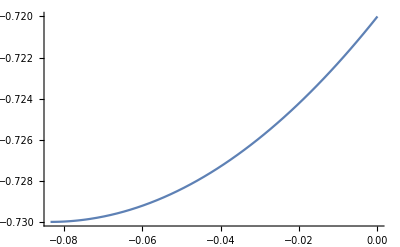
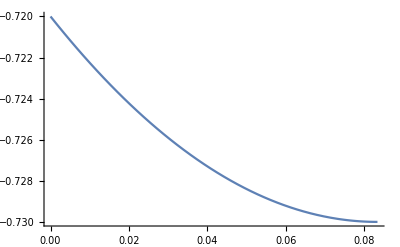

fsoc with different angles of Separeble-soliton q=0.20, soliton part

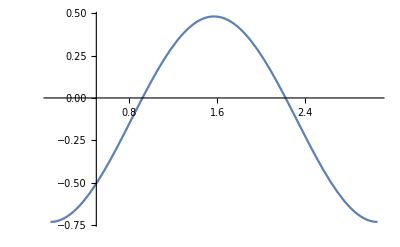

```mathematica
Clear[γ3,q,θ,θ0,θe,fsoc1,fsoc2,fsoc3,fsoc4];
γ3=q/(1+Abs[q]);
θ0=ArcSin[γ3/2];
fsoc1[θ_]=-1/2 (1+Abs[q])^2 Cos[2 θ]-(1+Abs[q])q Sin[θ];
fsoc2[θ_]=-1/2 (1+Abs[q])^2 Cos[2 (π-θ)]-(1+Abs[q])q Sin[π-θ];
Print[Style["fsoc with different angles of Separeble-soliton q=0.20, KLS-soliton part",18,Red]]
{Plot[fsoc1[θ]/.q->-0.20,{θ,(θ0/.q->-0.20),0}],Plot[fsoc1[θ]/.q->0.20,{θ,0,θ0/.q->0.20}]}
Print[Style["fsoc with different angles of Separeble-soliton q=0.20, soliton part",18,Red]]
{Plot[fsoc1[θ]/.q->0.20,{θ,(θ0/.q->0.20),π-(θ0/.q->0.20)}]}
```

```mathematica
N[1/8 π π 18]
18/2 17 (-1)
%+%%
```

22.2066

-153

-130.793

```mathematica
0.12*0.12
```

0.0144

```mathematica
N[1/8 π π 18 (1+0.12*0.12)]
18/2 17 (-1.26)
%+%%
```

22.5264

-192.78

-170.254

```mathematica
N[1/8 π π 18 (1+0.2*0.2)]
18/2 17 (-1.46)
%+%%
```

23.0949

-223.38

-200.285

```mathematica
N[1/(8 18) π π (1+0.2*0.2)]
 1/2(-1.46)
%+%%
```

0.0712805

-0.73

-0.65872

```mathematica
N[1/(8 18) π π (1+0.01 0.01)]
 1/2(-1.0)
%+%%
```

0.0685458

-0.5

-0.431454

```mathematica
θ0=ArcSin[q/(1-Abs[q])];
fLondon[q_]:=(π^2 dd)/(8 ξd)(1+Abs[q]^2)+(dd (dd-ξd))/(2 ξd^2) (-(1+Abs[q])^2 Cos[2Abs[θ0]]-2(1+Abs[q])Abs[q]Sin[Abs[θ0]])
ddfLondon[q_]:=1/dd^2 ((π^2 dd)/(8 ξd)(1+Abs[q]^2)+(dd (dd-ξd))/(2 ξd^2) (-(1+Abs[q])^2 Cos[2Abs[θ0]]-2(1+Abs[q])Abs[q]Sin[Abs[θ0]]))
ξd=1;dd=18 ξd;
Table[N[fLondon[q]],{q,0.0,0.2,0.01}]
Table[N[ddfLondon[q]],{q,0.0,0.2,0.01}]
```

{-130.793,-133.866,-136.961,-140.073,-143.198,-146.331,-149.466,-152.595,-155.711,-158.806,-161.87,-164.894,-167.867,-170.776,-173.608,-176.349,-178.981,-181.487,-183.848,-186.041,-188.045}

{-0.403683,-0.413166,-0.422718,-0.432324,-0.441971,-0.45164,-0.461314,-0.470971,-0.480588,-0.490141,-0.499599,-0.508934,-0.518109,-0.527088,-0.535829,-0.544286,-0.552409,-0.560144,-0.567431,-0.574202,-0.580386}